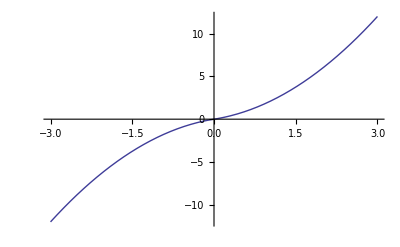

```mathematica
Plot[x(1+Abs[x]),{x,-3,3}]
```

```mathematica
D[x(1+Abs[x]),x]
```

1+Abs[x]+x Abs'[x]

```mathematica
D[Abs[x],x]
```

Abs'[x]

```mathematica
Cos[3*Pi]
```

-1

```mathematica
f[x_]=x(1+Abs[x]);
FourierTransform[f[x], x, ω]
```

-(2 ⅈ √(2/π))/ω^3

```mathematica
a=1/2L∫_-3^3 x(1+Abs[x])ⅆx
```

0

```mathematica
n=1;
b=1/L∫_-3^3 x(1+Abs[x])Cos[n*Pi*x/L]ⅆx
```

0

```mathematica
Clear[n]
```

```mathematica
c=1/L∫_-3^3 x(1+Abs[x])Sin[n*Pi*x/L]ⅆx
```

-(2 (2 L^2-2 L^2 Cos[(3 n π)/L]+12 n^2 π^2 Cos[(3 n π)/L]-7 L n π Sin[(3 n π)/L]))/(n^3 π^3)